```mathematica
(* This notebook contains examples for the PET-functions
 -ExtractMinDat-        extract mineral-chemical parameters
 -DataSymbols-          chose various plot symbols for data points and their size
 -TrianglePlot-         plot mineral-chemical data in a triangular diagram
 -XYPlot-               create a xy-plot of mineral-chemical data               *)
(* This top-cell must be run once before any example can be performed.  *)

(* Define the directory,where the PET-files reside (e.g. C:\Eigene Dateien\Pet) and load PET. *)$PetDirectory="C:\Dokumente und Einstellungen\dachsedgar\Eigene Dateien\Pet\Pet7.0";

SetDirectory[$PetDirectory];
DeclarePackage["DEFDAT`",{"Dataset"}];
Dataset[Dataset-> B88];
```

```mathematica
(* Example 1: use the PET-function -ExtractMinDat- to extract Al(VI) for white mica from the data file  "hs78b" *)

dat=ExtractMinDat[wm,"Al(VI)","hs78b"]
```

{{1.89589}}

Message from -CalcFormula-: creating file "hs78b.fu".

Message from -CalcFormula-: creating file "pet1.fu".

{{0.87958,0.87958},{1.89589,1.89589}}

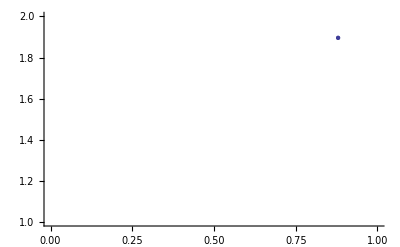

```mathematica
(* Example 2: use the PET-function -ExtractMinDat- to extract Al(IV) and Al(VI) for white mica from the data files  "hs78b" and "pet1"(containing an identical analsis of wm, therefore two identical valus are extracted and plotted as one point).
Use the Mathematica-function -ListPlot- to plot the data.   *)

CalcFormula["hs78b",CalcFormulaMode->{}];
CalcFormula["pet1",CalcFormulaMode->{}];
dat=ExtractMinDat[wm,{"Al(IV)","Al(VI)"},{"hs78b","pet1"}]
ListPlot[Transpose[dat],PlotRange->{{0,1},{1,2}}]
```

```mathematica
(* Example 3: use the PET-function -ExtractMinDat- to extract XFe for garnet from the data file
"pet1" (containing two grt-analyses with the labels "3c" and "4r", where c and r at the end indicate core and rim).
Use the option ExtractMinDatTexture to extract only the rim composition. *)

dat = ExtractMinDat[grt,"XFe","pet1",ExtractMinDatTexture->"r", ExtractMinDatTextureRange->{-1,-1}]
```

{{0.66343}}

```mathematica
(* Example 4: use the PET-function -ExtractMinDat- to extract SiO2 for amphibole from the data files
"pet1" and "pet2" for those analyses whose label ends with "mar" (for matrix-rim) *)

CalcFormula["pet2",CalcFormulaMode->{}];
file={"pet1","pet2"};
ExtractMinDat[amph,"SiO2",file, ExtractMinDatTexture->"mar",
								 ExtractMinDatTextureRange->{-3,-1},
								ExtractMinDatFile->"NewFile",
								ExtractMinDatMode->SearchFiles]
```

Message from -CalcFormula-: creating file "pet2.fu".

Message from -ExtractMinDat-: The file "NewFile_amph_mar" has been created.

```mathematica
(* Example 5: use the PET-function -ExtractMinDat- to combine all analyses from the data files
"hs78b","pet1" and "pet2" in one file named "NewFile" *)

file={"hs78b","pet1","pet2"};
ExtractMinDat[all,"SiO2",file,ExtractMinDatFile->"NewFile",
								ExtractMinDatMode->SearchFiles]
```

Message from -ExtractMinDat-: The file "NewFile_all" has been created.

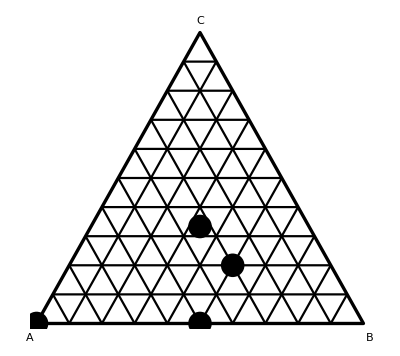

```mathematica
(* Example 7: Use the PET-function -TrianglePlot- to plot some data into the concentration triangle A-B-C *)

data = {{100,0,0},{50,50,0},{1/3,1/3,1/3},{30,50,20}};
t1=TrianglePlot[data,TrianglePlotSymbolShape->SymbolShapeDot, TrianglePlotSymbolSize->0.02, TrianglePlotGrid->TrianglePlotGridMesh,TrianglePlotAxesLabel->{"A","B","C"}]
```

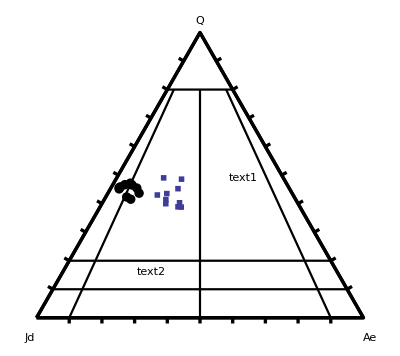

```mathematica
(* Example 8: Use the PET-function -TrianglePlot- to plot pyroxenes from file "pet2" into the 
triangle Jd-Ae-Q. "pet2" contains 20 analyses of zoned omphacites,10 with analyses labels
ending in "mar" (indicating "ma"trix "r"im compositions),10 ending in "mac" (indicating "ma"trix "c"-ore compositions).
Use triangles and dots as plot symbols,draw tick marks,use the\n
Na-pyroxene nomenclature grid and plot two text-labels into the triangle *)

(* first you must use the PET-function -ExtractMinDat- to extract the data with the specific textural position *)
d1=ExtractMinDat[cpx,{"MolJd","MolAe","MolQ"},"pet2",ExtractMinDatTexture->"mar",ExtractMinDatTextureRange->{-3,-1}];
d2=ExtractMinDat[cpx,{"MolJd","MolAe","MolQ"},"pet2",ExtractMinDatTexture->"mac",ExtractMinDatTextureRange->{-3,-1}];
t1=TrianglePlot[Transpose[d1],TrianglePlotSymbolShape->SymbolShapeSquare,TrianglePlotSymbolSize->0.02];
t2=TrianglePlot[Transpose[d2],TrianglePlotSymbolShape->SymbolShapeDot,TrianglePlotSymbolSize->0.008,TrianglePlotText->{Text["text1",Scaled[{0.67,0.5}],{1,0},{1,0}],Text["text2",Scaled[{0.4,0.19}],{1,0},{1,0}]},TrianglePlotTicks->TrianglePlotTicksYes,TrianglePlotGrid->TrianglePlotGridPx,TrianglePlotAxesLabel->{"Jd","Ae","Q"}];Show[t1,t2]
```

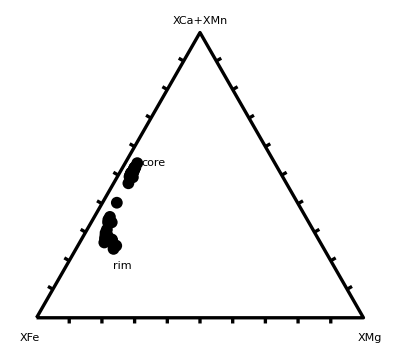

```mathematica
(* Example 9:  Triangle-plot for garnets  *)
{xfe,xmg,xca,xmn}=ExtractMinDat[grt,{"XFe","XMg","XCa","XMn"},"pet2"];
t1=TrianglePlot[Transpose[{xfe,xmg,xca+xmn}],TrianglePlotSymbolShape->SymbolShapeDot, TrianglePlotSymbolSize->0.01,TrianglePlotText->{Text["core",Scaled[{0.4,0.55}],{1,0},{1,0}], Text["rim",Scaled[{0.3,0.21}],{1,0},{1,0}]},
TrianglePlotTicks->TrianglePlotTicksYes,TrianglePlotAxesLabel->{"XFe","XMg", "XCa+XMn"}]
```

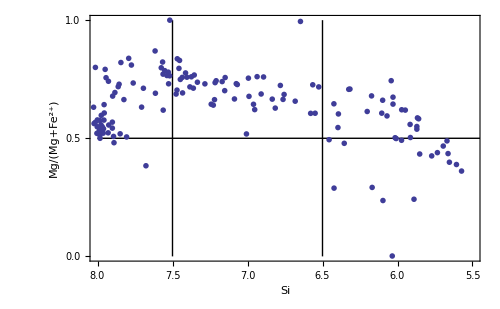

```mathematica
(* Example 10: Use the PET-function -XYPlot- to plot mineral-chemical data *)
(* Example 10a: calling XYPlot just specifying a file-name creates a xy-plot using default settings *)

XYPlot["pet2"]
```

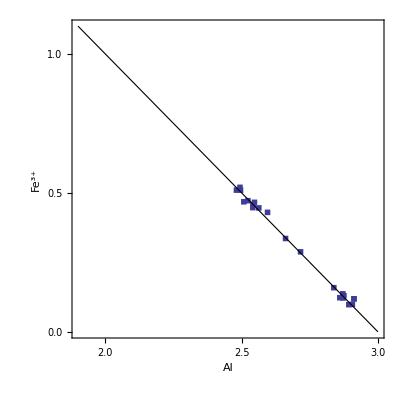

```mathematica
(* Example 10: Use the PET-function -XYPlot- to plot mineral-chemical data *)
(* Example 10b: change the plot-type to zoisite/epidote, use squares as data symbols enlarging their size  *)

XYPlot["pet2",XYPlotType->XYPlotTypeZoEp1,XYPlotSymbolShape->SymbolShapeSquare,XYPlotSymbolSize->0.02]
```

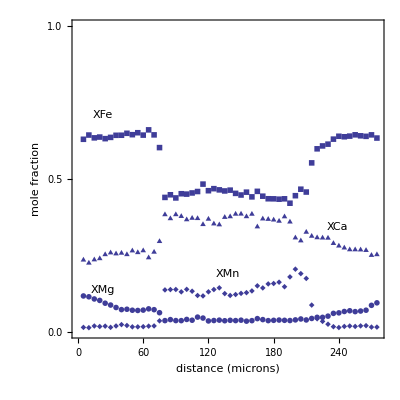

```mathematica
(* Example 10: Use the PET-function -XYPlot- to plot mineral-chemical data *)
(* Example 10c: create a garnet-zoning profile: use squares, dots, triangles and diamonds as data symbols,
	increase the x-spacing of the data points to 5 microns  *)

p1=XYPlot["pet2",XYPlotType->XYPlotTypeGrtProfileXFe,XYPlotSymbolShape->SymbolShapeSquare,
XYPlotTypeGrtProfileFactor->5];
p2=XYPlot["pet2",XYPlotType->XYPlotTypeGrtProfileXMg,XYPlotSymbolShape->SymbolShapeDot,
XYPlotTypeGrtProfileFactor->5];
p3=XYPlot["pet2",XYPlotType->XYPlotTypeGrtProfileXCa,XYPlotSymbolShape->SymbolShapeTriangle,
XYPlotTypeGrtProfileFactor->5];
p4=XYPlot["pet2",XYPlotType->XYPlotTypeGrtProfileXMn,XYPlotSymbolShape->SymbolShapeDiamond,
XYPlotTypeGrtProfileFactor->5];
Show[p1,p2,p3,p4]
```

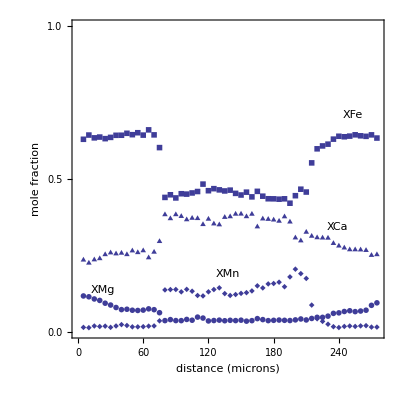

```mathematica
(* Example 10: Use the PET-function -XYPlot- to plot mineral-chemical data *)
(* Example 10c: as in 10b and change the positions of the XFe label by changing its coordinates in the option "XYPlotLabelPosition";
Note: XYPlotLabelPosition->{{0.1,0.7},{0.1,0.15},{0.85,0.35},{0.5,0.2}} are the default settings for labels XFe, XMg, XCa, XMn *)

p1=XYPlot["pet2",XYPlotType->XYPlotTypeGrtProfileXFe,XYPlotSymbolShape->SymbolShapeSquare,
XYPlotTypeGrtProfileFactor->5,XYPlotLabelPosition->{{0.9,0.7},{0.1,0.15},{0.85,0.35},{0.5,0.2}}];
p2=XYPlot["pet2",XYPlotType->XYPlotTypeGrtProfileXMg,XYPlotSymbolShape->SymbolShapeDot,
XYPlotTypeGrtProfileFactor->5];
p3=XYPlot["pet2",XYPlotType->XYPlotTypeGrtProfileXCa,XYPlotSymbolShape->SymbolShapeTriangle,
XYPlotTypeGrtProfileFactor->5];
p4=XYPlot["pet2",XYPlotType->XYPlotTypeGrtProfileXMn,XYPlotSymbolShape->SymbolShapeDiamond,
XYPlotTypeGrtProfileFactor->5];
Show[p1,p2,p3,p4]
```

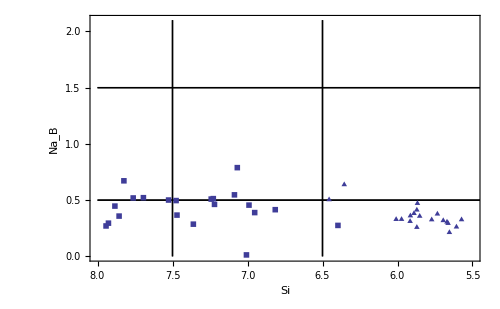

```mathematica
(* Example 10: Use the PET-function -XYPlot- to plot mineral-chemical data *)
(* Example 10d: draw a Na[B] versus Si diagram for amphibole and differentiate amphiboles by their analyses labels;
	(amphiboles in "pet2" with labels ending in "sgu" are rims around eclogite-garnet,
	those with labels ending in "syu" are symplectite-amphiboles *)
p1 = XYPlot["pet2",XYPlotType->XYPlotTypeAmph2,XYPlotTexture->"sgu",XYPlotSymbolShape->SymbolShapeTriangle,XYPlotSymbolSize->0.03];
p2 = XYPlot["pet2",XYPlotType->XYPlotTypeAmph2,XYPlotTexture->"syu",XYPlotSymbolShape->SymbolShapeSquare,XYPlotSymbolSize->0.025];
Show[p1,p2]
```